# Vector mode in D=4

```mathematica
(*z=1/r*)
X={v,z,x1,x2};
```

```mathematica
d=4;
```

```mathematica
G=1/z^2{{-f[z] z^2,-1,ϵ 1/2 htx[z] E^(-I ω v+I k x2),(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0},{-1, 0,0,0},
{ϵ 1/2 htx[z] E^(-I ω v+I k x2),0,1,ϵ 1/2 hyx[z] E^(-I ω v+I k x2)},{(*ϵ 1/2 hty[z] E^(-I ω v+I k x3)*)0,0, ϵ 1/2 hyx[z] E^(-I ω v+I k x2),1(*ϵ 1/2 hzy[z] E^(-I ω (t- Integrate[1/f[z],z])+I k x3)*)}}(*/.ϵ->0*)(*/.z->1/r*);
```

```mathematica
G//MatrixForm
```

(-f[z] | -1/z^2 | (ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0
-1/z^2 | 0 | 0 | 0
(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2) | 0 | 1/z^2 | (ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)
0 | 0 | (ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2) | 1/z^2)

```mathematica
G
```

{{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}}

```mathematica
kn
```

kn

```mathematica
IG=Inverse[G];
IG/.ϵ->0//MatrixForm
```

(0 | -z^2 | 0 | 0
-z^2 | z^4 f[z] | 0 | 0
0 | 0 | z^2 | 0
0 | 0 | 0 | z^2)

```mathematica
IG.G//Simplify
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

```mathematica
Γ=Normal[Series[Table[1/2*Sum[IG[[i,l]]*(D[G[[j,l]],X[[k1]]]+D[G[[k1,l]],X[[j]]]-D[G[[j,k1]],X[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k1,1,d}],{ϵ,0,1}]];
```

```mathematica
Ric=Table[Sum[D[Γ[[k1,i,j]],X[[k1]]]-D[Γ[[k1,k1,i]],X[[j]]]+Sum[Γ[[q1,q1,k1]]Γ[[k1,i,j]]-Γ[[q1,i,k1]]Γ[[k1,q1,j]],{q1,1,d}],{k1,1,d}],{i,1,d},{j,1,d}](*Table[Sum[D[Γ[[i,j,k1]],X[[i]]]-D[Γ[[i,k1,i]],X[[j]]]+Sum[Γ[[i,i,p]]Γ[[p,j,k1]]-Γ[[i,j,p]]Γ[[p,i,k1]],{p,1,d}],{i,1,d}],{j,1,d},{k1,1,d}]*);
R=Normal[Series[Sum[IG[[i,j]]Ric[[i,j]],{i,1,d},{j,1,d}],{ϵ,0,1}]];
```

```mathematica
Eing=Table[Ric[[i,j]]-1/2 R*G[[i,j]],{i,1,d},{j,1,d}];
```

```mathematica
Λ = -(d-1)(d-2)/2;
```

```mathematica
EinEq=Normal[Series[Eing+ Λ G,{ϵ,0,1}]]/.f->Function[z,1/z^2(1-z^3/zh^3)](*/.f->Function[z,1-z^4/zh^4]*)(*/.zh->1*);
EinEq/.ϵ->0//Expand//Simplify//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

```mathematica
zh
```

zh

I output the three equations

```mathematica
EinEq[[1,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand
EinEq[[3,4]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal(*//Collect[#,{htx'[z], hzx'[z]}]&*)
```

(ⅇ^(ⅈ (k x2-v ω)) ϵ (k^2 z zh^3 htx[z]+k z zh^3 ω hyx[z]-2 z^3 htx'[z]+2 zh^3 htx'[z]-ⅈ z zh^3 ω htx'[z]+z^4 htx''[z]-z zh^3 htx''[z]))/(4 z zh^3)

(ⅇ^(ⅈ (k x2-v ω)) ϵ htx'[z])/(2 z)+1/4 ⅈ ⅇ^(ⅈ (k x2-v ω)) k ϵ hyx'[z]-1/4 ⅇ^(ⅈ (k x2-v ω)) ϵ htx''[z]

(ⅇ^(ⅈ (k x2-v ω)) ϵ (2 ⅈ k zh^3 htx[z]+2 ⅈ zh^3 ω hyx[z]-ⅈ k z zh^3 htx'[z]+z^3 hyx'[z]+2 zh^3 hyx'[z]-2 ⅈ z zh^3 ω hyx'[z]+z^4 hyx''[z]-z zh^3 hyx''[z]))/(4 z zh^3)

I eliminate the first derivative of htx

```mathematica
htppRule=Solve[(EinEq[[2,3]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal//Expand)==0,htx''[z]]//Flatten
```

{htx''[z]→(2 htx'[z]+ⅈ k z hyx'[z])/z}

I look for differential equation for hzx and htx

```mathematica
Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,4]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hyx''[z],htx'[z]}]//Simplify
```

{{hyx''[z]→(k zh^3 (k^2 z-2 ⅈ ω) htx[z]+zh^3 (k^2 z-2 ⅈ ω) ω hyx[z]+ⅈ (k^2 (z^4-z zh^3)+ω (ⅈ z^3+2 ⅈ zh^3+2 z zh^3 ω)) hyx'[z])/(z (z^3-zh^3) ω),htx'[z]→k (-(ⅈ k htx[z])/ω-ⅈ hyx[z]+((z^3-zh^3) hyx'[z])/(zh^3 ω))}}

The sln below is obtained solving for each of the component of EinEq

```mathematica
sln=Solve[{0==EinEq[[1,3]]/.htppRule[[1]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal,
0==EinEq[[3,4]]//Series[#,{ϵ,0,1}]&(*//UpperTriangularize*)//Simplify//Normal},{hyx''[z],htx'[z]}]//Simplify//Flatten
```

{hyx''[z]→(k zh^3 (k^2 z-2 ⅈ ω) htx[z]+zh^3 (k^2 z-2 ⅈ ω) ω hyx[z]+ⅈ (k^2 (z^4-z zh^3)+ω (ⅈ z^3+2 ⅈ zh^3+2 z zh^3 ω)) hyx'[z])/(z (z^3-zh^3) ω),htx'[z]→k (-(ⅈ k htx[z])/ω-ⅈ hyx[z]+((z^3-zh^3) hyx'[z])/(zh^3 ω))}

```mathematica
eqns=sln[[All,1]]-sln[[All,2]]
```

{-(k zh^3 (k^2 z-2 ⅈ ω) htx[z]+zh^3 (k^2 z-2 ⅈ ω) ω hyx[z]+ⅈ (k^2 (z^4-z zh^3)+ω (ⅈ z^3+2 ⅈ zh^3+2 z zh^3 ω)) hyx'[z])/(z (z^3-zh^3) ω)+hyx''[z],htx'[z]-k (-(ⅈ k htx[z])/ω-ⅈ hyx[z]+((z^3-zh^3) hyx'[z])/(zh^3 ω))}

```mathematica
(*eqns={(k z ω htx[z]+(-1+z^4) (3 ⅈ ω hzx[z]+(3+z^4-2 ⅈ z ω) hzx'[z]))/(z (-1+z^4)^2)+hzx''[z],(k z ω hty[z]+(-1+z^4) (3 ⅈ ω hzy[z]+(3+z^4-2 ⅈ z ω) hzy'[z]))/(z (-1+z^4)^2)+hzy''[z],-(ⅈ ω htx[z])/(-1+z^4)+ⅈ k hzx[z]+htx'[z]-(k (-1+z^4) hzx'[z])/ω,-(ⅈ ω hty[z])/(-1+z^4)+ⅈ k hzy[z]+hty'[z]-(k (-1+z^4) hzy'[z])/ω};*)
```

### massless KG, equation

Doubt:how to know whit which order we start the expansion? Why htx and hty start from 1 and the pure spatial entries start from 0?

```mathematica
NHexpansion={htx->Function[z, Sum[c[1,i](zh-z)^i,{i,0,3}]](*,hty->Function[z, Sum[c[2,i](1-z)^i,{i,1,3}]]*),hyx->Function[z, Sum[c[2,i](zh-z)^i,{i,0,3}]](*,hzy->Function[z, Sum[c[4,i](1-z)^i,{i,0,3}]]*)};
```

```mathematica
(*2 constants.*)
replNH={c[1,1]->(ⅈ k (k c[1,0]+ω c[2,0]))/ω,c[2,1]->-(ⅈ (k^2 zh-2 ⅈ ω) (k c[1,0]+ω c[2,0]))/(ω (3 ⅈ+2 zh ω)),c[1,2]->-(k (-6+k^2 zh^2+2 ⅈ zh ω) (k c[1,0]+ω c[2,0]))/(2 zh ω (3 ⅈ+2 zh ω)),c[2,2]->((k^4 zh^3-6 ⅈ ω) (k c[1,0]+ω c[2,0]))/(4 zh ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω)),c[1,3]->(k (-ⅈ (-6+k^2 zh^2)^2+2 zh (-9+2 k^2 zh^2) ω) (k c[1,0]+ω c[2,0]))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω)),c[2,3]->((ⅈ k^4 zh^3+6 ω) (6+k^2 zh^2+2 ⅈ zh ω) (k c[1,0]+ω c[2,0]))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω) (9 ⅈ+2 zh ω))};
```

```mathematica
NI=2;
cInd=NI;
```

```mathematica
Solve[0==Series[{(zh-z)^2(*,(1-z)^2,(1-z)*),(zh-z)}eqns(*/.zh->1*)/.NHexpansion//.replNH,{z,zh,NI}]//Normal//Simplify,Table[c[i,cInd],{i,1,2}]]//FullSimplify
```

{}

```mathematica
0==Series[{(zh-z)^2(*,(1-z)^2,(1-z)*),(zh-z)}eqns(*/.zh->1*)/.NHexpansion//.replNH,{z,zh,NI}]//FullSimplify
```

{((k^4 zh^3-6 ⅈ ω) (-ⅈ k^4 zh^3+90 ω+4 k^2 zh (-6 ⅈ+zh ω)) (k c[1,0]+ω c[2,0]) (z-zh)^4)/(36 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω) (9 ⅈ+2 zh ω))+O[z-zh]^5,O[z-zh]^4}==0

```mathematica
UVexpansion={htx->Function[z, Sum[b[1,i] z^i,{i,0,8}]],hyx->Function[z, Sum[b[2,i] z^i,{i,0,8}]]};
```

```mathematica
(*4 constants in the UV (2 vevs and 2 sources), 2 constants in the IR and of course ω ---> total 7 constants. If we set all the sources to zero we are left with a total of 5 constants, oout of which 1 can be set to 1 using the linearity of the equations... so, effectively, we have 4 constants. But the problem requires 6 integration constants! Explanation: both sources will be non-zero up to gauge.*)sub={b[1,0]->ctx, b[2,0]->cyx, b[1,3]->vty,b[2,3]->-(ω b[1,3])/k+1/6 ⅈ (k^3 b[1,0]+k^2 ω b[2,0])};
repl={b[1,1]->0,b[2,1]->-ⅈ (k b[1,0]+ω b[2,0]),b[1,2]->1/2 (-k^2 b[1,0]-k ω b[2,0]),b[2,2]->0,b[2,3]->-(ω b[1,3])/k+1/6 ⅈ (k^3 b[1,0]+k^2 ω b[2,0]),b[1,4]->1/8 (-k^4 b[1,0]-6 ⅈ ω b[1,3]-k^3 ω b[2,0]),b[2,4]->-1/(12 k zh^3)(3 ⅈ k^2 b[1,0]-2 k^4 zh^3 ω b[1,0]+3 ⅈ k^2 zh^3 b[1,3]-12 ⅈ zh^3 ω^2 b[1,3]+3 ⅈ k ω b[2,0]-2 k^3 zh^3 ω^2 b[2,0]),b[1,5]->-1/(30 zh^3)(-3 k^2 b[1,0]-2 ⅈ k^4 zh^3 ω b[1,0]-3 k^2 zh^3 b[1,3]+12 zh^3 ω^2 b[1,3]-3 k ω b[2,0]-2 ⅈ k^3 zh^3 ω^2 b[2,0]),b[2,5]->-1/(40 k zh^3)(-ⅈ k^6 zh^3 b[1,0]+6 k^2 ω b[1,0]+4 ⅈ k^4 zh^3 ω^2 b[1,0]+12 k^2 zh^3 ω b[1,3]-24 zh^3 ω^3 b[1,3]-ⅈ k^5 zh^3 ω b[2,0]+6 k ω^2 b[2,0]+4 ⅈ k^3 zh^3 ω^3 b[2,0]),b[1,6]->-1/(144 zh^3)(k^6 zh^3 b[1,0]+6 ⅈ k^2 ω b[1,0]-4 k^4 zh^3 ω^2 b[1,0]+12 ⅈ k^2 zh^3 ω b[1,3]-24 ⅈ zh^3 ω^3 b[1,3]+k^5 zh^3 ω b[2,0]+6 ⅈ k ω^2 b[2,0]-4 k^3 zh^3 ω^3 b[2,0]),b[2,6]->-1/(180 k zh^3)(-12 ⅈ k^4 b[1,0]-4 k^6 zh^3 ω b[1,0]-12 ⅈ k^2 ω^2 b[1,0]+8 k^4 zh^3 ω^3 b[1,0]+3 ⅈ k^4 zh^3 b[1,3]+90 ω b[1,3]-36 ⅈ k^2 zh^3 ω^2 b[1,3]+48 ⅈ zh^3 ω^4 b[1,3]-12 ⅈ k^3 ω b[2,0]-4 k^5 zh^3 ω^2 b[2,0]-12 ⅈ k ω^3 b[2,0]+8 k^3 zh^3 ω^4 b[2,0])}//Flatten(*b[1,1]->0,b[2,1]->-ⅈ (k b[1,0]+ω b[2,0]),b[1,2]->-1/4 k (k b[1,0]+ω b[2,0]),b[2,2]->-1/4 ω (k b[1,0]+ω b[2,0]),b[1,3]->1/6 ⅈ k ω (k b[1,0]+ω b[2,0]),b[2,3]->1/12 ⅈ (k^2-ω^2) (k b[1,0]+ω b[2,0]),b[1,5]->-4/5 ⅈ vzx ω,b[2,5]->-(ⅈ vzx (k^2-5 ω^2))/(5 k),b[1,6]->1/12 vzx (k^2-5 ω^2),b[2,6]->-1/4 k vzx ω+(7 vzx ω^3)/(12 k)*)(*/.sub*);
```

```mathematica
NN=6;
```

```mathematica
Solve[{0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,NN}]//Normal)[[1]],0==(Series[{z,1}eqns/.UVexpansion/.repl(*/.sub*),{z,0,NN}]//Normal)[[2]]},Table[b[i,

1+NN],{i,1,2}]]
```

{{b[1,7]→-1/(840 zh^3)(12 k^4 b[1,0]-4 ⅈ k^6 zh^3 ω b[1,0]+12 k^2 ω^2 b[1,0]+8 ⅈ k^4 zh^3 ω^3 b[1,0]-3 k^4 zh^3 b[1,3]+90 ⅈ ω b[1,3]+36 k^2 zh^3 ω^2 b[1,3]-48 zh^3 ω^4 b[1,3]+12 k^3 ω b[2,0]-4 ⅈ k^5 zh^3 ω^2 b[2,0]+12 k ω^3 b[2,0]+8 ⅈ k^3 zh^3 ω^4 b[2,0]),b[2,7]→-1/(1008 k zh^6)(144 ⅈ k^2 b[1,0]-ⅈ k^8 zh^6 b[1,0]-114 k^4 zh^3 ω b[1,0]+12 ⅈ k^6 zh^6 ω^2 b[1,0]-24 k^2 zh^3 ω^3 b[1,0]-16 ⅈ k^4 zh^6 ω^4 b[1,0]+144 ⅈ k^2 zh^3 b[1,3]+18 k^4 zh^6 ω b[1,3]-756 ⅈ zh^3 ω^2 b[1,3]-96 k^2 zh^6 ω^3 b[1,3]+96 zh^6 ω^5 b[1,3]+144 ⅈ k ω b[2,0]-ⅈ k^7 zh^6 ω b[2,0]-114 k^3 zh^3 ω^2 b[2,0]+12 ⅈ k^5 zh^6 ω^3 b[2,0]-24 k zh^3 ω^4 b[2,0]-16 ⅈ k^3 zh^6 ω^5 b[2,0])}}

#### Constrains on sources

```mathematica
nc=4;
```

```mathematica
exponential=Exp[-I ω  v(*(t- Integrate[1/f[z],z])*)] ⅇ^(ⅈ k x2);
```

```mathematica
ξup=exponential ϵ{0ζ1+0Sum[ζζ1[j] z^j,{j,1,nc}],1/z (ζ2 +Sum[ζζ2[j] z^j,{j,1,nc}]),ζ3+Sum[ζζ3[j] z^j,{j,1,nc}], ζ4+Sum[ζζ4[j] z^j,{j,1,nc}]};
ξ=G.ξup;
```

```mathematica
ξup
```

{0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ (ζ2+z ζζ2[1]+z^2 ζζ2[2]+z^3 ζζ2[3]+z^4 ζζ2[4]))/z,ⅇ^(ⅈ k x2-ⅈ v ω) ϵ (ζ3+z ζζ3[1]+z^2 ζζ3[2]+z^3 ζζ3[3]+z^4 ζζ3[4]),ⅇ^(ⅈ k x2-ⅈ v ω) ϵ (ζ4+z ζζ4[1]+z^2 ζζ4[2]+z^3 ζζ4[3]+z^4 ζζ4[4])}

```mathematica
Dξ=Table[1/2(D[ξ[[i]],X[[j]]]+D[ξ[[j]],X[[i]]])-Sum[Γ[[kk,i,j]] ξ[[kk]],{kk,1,nc}],{i,1,nc},{j,1,nc}];
```

```mathematica
Dξ2=Table[(D[ξup[[j]],X[[i]]])+Sum[Γ[[j,i,kk]] ξup[[kk]],{kk,1,nc}],{i,1,nc},{j,1,nc}];
```

```mathematica
subg={};
```

```mathematica
GG=Coefficient[Normal[Series[Simplify[2 Dξ]+G,{ϵ,0,1}]]/.f->Function[z,1-z^3/zh^3](*/.zh->1*),ϵ];
```

```mathematica
(**)Normal[Series[Simplify[1/exponential GG]/.f->Function[z,1-z^4/zh^4]/.zh->1/.UVexpansion/.sub/.repl,{z,0,2}]]/.l->1 /.{ζ4->(ⅈ czy)/(2 k),ζ3->(ⅈ czx)/(2 k),ζζ3[1]->(czx ω)/(2 k),ζζ4[1]->(czy ω)/(2 k),ζ5->0, ζ2->0,ζζ2[1]->0,ζζ5[1]->0,ζζ2[2]->0,ζζ2[3]->0,ζζ2[4]->0,ζζ5[2]->0,ζζ5[3]->0,ζζ3[2]->-(ⅈ czx ω^2)/(4 k),ζζ4[2]->-(ⅈ czy ω^2)/(4 k),ζζ3[3]->-(czx ω^3)/(12 k),ζζ4[3]->-(czy ω^3)/(12 k),ζζ2[5]->0,ζζ5[4]->0,ζζ5[5]->0,ζζ3[4]->(ⅈ czx ω^4)/(48 k),ζζ4[4]->(ⅈ czy ω^4)/(48 k),ζζ3[5]->(czx ω (24+ω^4))/(240 k),ζζ4[5]->(czy ω (24+ω^4))/(240 k)}//FullSimplify//Factor//MatrixForm
```

(0 | 0 | -(-24 ctx k-24 k vty z^3-24 czx ω+24 ⅈ czx z ω^2+12 czx z^2 ω^3-4 ⅈ czx z^3 ω^4-czx z^4 ω^5+12 k^3 z^2 b[1,0]+3 k^5 z^4 b[1,0]+18 ⅈ k z^4 ω b[1,3]+12 k^2 z^2 ω b[2,0]+3 k^4 z^4 ω b[2,0])/(48 k z^2) | (czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2)
0 | 0 | (czx ω (6-6 ⅈ z ω-3 z^2 ω^2+ⅈ z^3 ω^3))/(12 k z^2) | (czy ω (6-6 ⅈ z ω-3 z^2 ω^2+ⅈ z^3 ω^3))/(12 k z^2)
-(-24 ctx k-24 k vty z^3-24 czx ω+24 ⅈ czx z ω^2+12 czx z^2 ω^3-4 ⅈ czx z^3 ω^4-czx z^4 ω^5+12 k^3 z^2 b[1,0]+3 k^5 z^4 b[1,0]+18 ⅈ k z^4 ω b[1,3]+12 k^2 z^2 ω b[2,0]+3 k^4 z^4 ω b[2,0])/(48 k z^2) | (czx ω (6-6 ⅈ z ω-3 z^2 ω^2+ⅈ z^3 ω^3))/(12 k z^2) | 0 | -(-24 cyx k zh^3+24 czx k zh^3-24 ⅈ czx k z zh^3 ω-12 czx k z^2 zh^3 ω^2+4 ⅈ czx k z^3 zh^3 ω^3+czx k z^4 zh^3 ω^4+6 ⅈ k^2 z^4 b[1,0]+24 ⅈ k^2 z zh^3 b[1,0]-4 ⅈ k^4 z^3 zh^3 b[1,0]-4 k^4 z^4 zh^3 ω b[1,0]+6 ⅈ k^2 z^4 zh^3 b[1,3]+24 z^3 zh^3 ω b[1,3]-24 ⅈ z^4 zh^3 ω^2 b[1,3]+6 ⅈ k z^4 ω b[2,0]+24 ⅈ k z zh^3 ω b[2,0]-4 ⅈ k^3 z^3 zh^3 ω b[2,0]-4 k^3 z^4 zh^3 ω^2 b[2,0])/(48 k z^2 zh^3)
(czy ω (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(48 k z^2) | (czy ω (6-6 ⅈ z ω-3 z^2 ω^2+ⅈ z^3 ω^3))/(12 k z^2) | -(-24 cyx k zh^3+24 czx k zh^3-24 ⅈ czx k z zh^3 ω-12 czx k z^2 zh^3 ω^2+4 ⅈ czx k z^3 zh^3 ω^3+czx k z^4 zh^3 ω^4+6 ⅈ k^2 z^4 b[1,0]+24 ⅈ k^2 z zh^3 b[1,0]-4 ⅈ k^4 z^3 zh^3 b[1,0]-4 k^4 z^4 zh^3 ω b[1,0]+6 ⅈ k^2 z^4 zh^3 b[1,3]+24 z^3 zh^3 ω b[1,3]-24 ⅈ z^4 zh^3 ω^2 b[1,3]+6 ⅈ k z^4 ω b[2,0]+24 ⅈ k z zh^3 ω b[2,0]-4 ⅈ k^3 z^3 zh^3 ω b[2,0]-4 k^3 z^4 zh^3 ω^2 b[2,0])/(48 k z^2 zh^3) | -(czy (24-24 ⅈ z ω-12 z^2 ω^2+4 ⅈ z^3 ω^3+z^4 ω^4))/(24 z^2))

```mathematica
ξRules={ζ4->(ⅈ czy)/(2 k),ζ3->(ⅈ czx)/(2 k),ζζ3[1]->(czx ω)/(2 k),ζζ4[1]->(czy ω)/(2 k),ζ5->0, ζ2->0,ζζ2[1]->0,ζζ5[1]->0,ζζ2[2]->0,ζζ2[3]->0,ζζ2[4]->0,ζζ5[2]->0,ζζ5[3]->0,ζζ3[2]->-(ⅈ czx ω^2)/(4 k),ζζ4[2]->-(ⅈ czy ω^2)/(4 k),ζζ3[3]->-(czx ω^3)/(12 k),ζζ4[3]->-(czy ω^3)/(12 k),ζζ2[5]->0,ζζ5[4]->0,ζζ5[5]->0,ζζ3[4]->(ⅈ czx ω^4)/(48 k),ζζ4[4]->(ⅈ czy ω^4)/(48 k),ζζ3[5]->(czx ω (24+ω^4))/(240 k),ζζ4[5]->(czy ω (24+ω^4))/(240 k)};
```

```mathematica
ξup/.ξRules
```

{0,0,ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ((ⅈ czx)/(2 k)+(czx z ω)/(2 k)-(ⅈ czx z^2 ω^2)/(4 k)-(czx z^3 ω^3)/(12 k)+(ⅈ czx z^4 ω^4)/(48 k)),ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ((ⅈ czy)/(2 k)+(czy z ω)/(2 k)-(ⅈ czy z^2 ω^2)/(4 k)-(czy z^3 ω^3)/(12 k)+(ⅈ czy z^4 ω^4)/(48 k))}

```mathematica
vevTransformation={vzx->vzx-(czx ω^4)/24,vzy->vzy-(czy ω^4)/24};
```

```mathematica
(*both sources can be removed by a gauge transformation*)
Solve[{ζ4==(ⅈ czy)/(2 k),ζ3==(ⅈ czx)/(2 k)},{czy,czx}]
```

{{czy→-2 ⅈ k ζ4,czx→-2 ⅈ k ζ3}}

### Shooting Method

```mathematica
eqns
```

{-1/(z (z^3-zh^3) ω)(k zh^3 (k^2 z-2 ⅈ ω) htx[z]+zh^3 (k^2 z-2 ⅈ ω) ω hyx[z]+ⅈ (k^2 (z^4-z zh^3)+ω (ⅈ z^3+2 ⅈ zh^3+2 z zh^3 ω)) hyx'[z])+hyx''[z],htx'[z]-k (-(ⅈ k htx[z])/ω-ⅈ hyx[z]+((z^3-zh^3) hyx'[z])/(zh^3 ω))}

```mathematica
eqnlist[ω_,k_]:={-1/(z (z^3-zh^3) ω)(k zh^3 (k^2 z-2 ⅈ ω) htx[z]+zh^3 (k^2 z-2 ⅈ ω) ω hyx[z]+ⅈ (k^2 (z^4-z zh^3)+ω (ⅈ z^3+2 ⅈ zh^3+2 z zh^3 ω)) hyx'[z])+hyx''[z],htx'[z]-k (-(ⅈ k htx[z])/ω-ⅈ hyx[z]+((z^3-zh^3) hyx'[z])/(zh^3 ω))};
```

Parameters: 
General: ω k zh
Near Horizon: c1
Infinity: 2 Sources (cyx, ctx), 1 VeV (vty)

```mathematica
c1
```

c1

```mathematica
(htx[z]/.NHexpansion/.replNH/.c[1,0]->c1/.c[2,0]->c2)//Collect[#,{  (zh-z)},Simplify]&
(hyx[z]/.NHexpansion//.replNH/.c[1,0]->c1/.c[2,0]->c2)//Collect[#,{  (zh-z)},Simplify]&
(htx[z]/.UVexpansion/.repl/. b[1,7]->0/. b[1,8]->0//.sub)//Collect[#,{  (z)},Simplify]&
(hyx[z]/.UVexpansion/.repl/. b[2,7]->0/. b[2,8]->0//.sub)//Collect[#,{  (z)},Simplify]&
```

c1+(ⅈ k (-z+zh) (c1 k+c2 ω))/ω-(k (-z+zh)^2 (c1 k+c2 ω) (-6+k^2 zh^2+2 ⅈ zh ω))/(2 zh ω (3 ⅈ+2 zh ω))+(k (-z+zh)^3 (c1 k+c2 ω) (-ⅈ (-6+k^2 zh^2)^2+2 zh (-9+2 k^2 zh^2) ω))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω))

c2-(ⅈ (-z+zh) (k^2 zh-2 ⅈ ω) (c1 k+c2 ω))/(ω (3 ⅈ+2 zh ω))+((-z+zh)^2 (k^4 zh^3-6 ⅈ ω) (c1 k+c2 ω))/(4 zh ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω))+((-z+zh)^3 (ⅈ k^4 zh^3+6 ω) (c1 k+c2 ω) (6+k^2 zh^2+2 ⅈ zh ω))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω) (9 ⅈ+2 zh ω))

ctx+vty z^3-1/2 k z^2 (ctx k+cyx ω)+1/8 z^4 (-ctx k^4-(cyx k^3+6 ⅈ vty) ω)+(z^5 (3 ctx k^2+3 k^2 vty zh^3+3 cyx k ω+2 ⅈ ctx k^4 zh^3 ω+2 ⅈ cyx k^3 zh^3 ω^2-12 vty zh^3 ω^2))/(30 zh^3)+(z^6 (-12 ⅈ vty zh^3 ω (k^2-2 ω^2)+cyx ω (-k^5 zh^3-6 ⅈ k ω+4 k^3 zh^3 ω^2)-ctx (k^6 zh^3+6 ⅈ k^2 ω-4 k^4 zh^3 ω^2)))/(144 zh^3)

cyx-ⅈ z (ctx k+cyx ω)+(ⅈ z^3 (ctx k^4+cyx k^3 ω+6 ⅈ vty ω))/(6 k)+1/12 z^4 (-(3 ⅈ k (ctx+vty zh^3))/zh^3+2 ctx k^3 ω-(3 ⅈ cyx ω)/zh^3+2 cyx k^2 ω^2+(12 ⅈ vty ω^2)/k)+(ⅈ z^5 (12 ⅈ vty zh^3 ω (k^2-2 ω^2)+cyx ω (k^5 zh^3+6 ⅈ k ω-4 k^3 zh^3 ω^2)+ctx (k^6 zh^3+6 ⅈ k^2 ω-4 k^4 zh^3 ω^2)))/(40 k zh^3)+(z^6 (-3 ⅈ k^4 vty zh^3+4 cyx k^5 zh^3 ω^2+36 ⅈ k^2 vty zh^3 ω^2+12 ⅈ cyx k ω^3+4 cyx k^3 ω (3 ⅈ-2 zh^3 ω^3)+6 vty ω (-15-8 ⅈ zh^3 ω^3)+4 ctx (k^6 zh^3 ω+3 ⅈ k^2 ω^2+k^4 (3 ⅈ-2 zh^3 ω^3))))/(180 k zh^3)

```mathematica
NHhtx[c1_,c2_, ω_,k_][z_]:=c1+(ⅈ k (-z+zh) (c1 k+c2 ω))/ω-(k (-z+zh)^2 (c1 k+c2 ω) (-6+k^2 zh^2+2 ⅈ zh ω))/(2 zh ω (3 ⅈ+2 zh ω))+(k (-z+zh)^3 (c1 k+c2 ω) (-ⅈ (-6+k^2 zh^2)^2+2 zh (-9+2 k^2 zh^2) ω))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω));
NHhzx[c1_,c2_, ω_,k_][z_]:=c2-(ⅈ (-z+zh) (k^2 zh-2 ⅈ ω) (c1 k+c2 ω))/(ω (3 ⅈ+2 zh ω))+((-z+zh)^2 (k^4 zh^3-6 ⅈ ω) (c1 k+c2 ω))/(4 zh ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω))+((-z+zh)^3 (ⅈ k^4 zh^3+6 ω) (c1 k+c2 ω) (6+k^2 zh^2+2 ⅈ zh ω))/(12 zh^2 ω (3 ⅈ+zh ω) (3 ⅈ+2 zh ω) (9 ⅈ+2 zh ω));
```

```mathematica
Ashtx[ctx_,cyx_,vty_, ω_,k_][z_]:=ctx+vty z^3-1/2 k z^2 (ctx k+cyx ω)+1/8 z^4 (-ctx k^4-(cyx k^3+6 ⅈ vty) ω)+1/(30 zh^3)z^5 (3 ctx k^2+3 k^2 vty zh^3+3 cyx k ω+2 ⅈ ctx k^4 zh^3 ω+2 ⅈ cyx k^3 zh^3 ω^2-12 vty zh^3 ω^2)+1/(144 zh^3)z^6 (-12 ⅈ vty zh^3 ω (k^2-2 ω^2)+cyx ω (-k^5 zh^3-6 ⅈ k ω+4 k^3 zh^3 ω^2)-ctx (k^6 zh^3+6 ⅈ k^2 ω-4 k^4 zh^3 ω^2));
Ashzx[ctx_,cyx_,vty_, ω_,k_][z_]:=cyx-ⅈ z (ctx k+cyx ω)+(ⅈ z^3 (ctx k^4+cyx k^3 ω+6 ⅈ vty ω))/(6 k)+1/12 z^4 (-(3 ⅈ k (ctx+vty zh^3))/zh^3+2 ctx k^3 ω-(3 ⅈ cyx ω)/zh^3+2 cyx k^2 ω^2+(12 ⅈ vty ω^2)/k)+1/(40 k zh^3)ⅈ z^5 (12 ⅈ vty zh^3 ω (k^2-2 ω^2)+cyx ω (k^5 zh^3+6 ⅈ k ω-4 k^3 zh^3 ω^2)+ctx (k^6 zh^3+6 ⅈ k^2 ω-4 k^4 zh^3 ω^2))+1/(180 k zh^3)z^6 (-3 ⅈ k^4 vty zh^3+4 cyx k^5 zh^3 ω^2+36 ⅈ k^2 vty zh^3 ω^2+12 ⅈ cyx k ω^3+4 cyx k^3 ω (3 ⅈ-2 zh^3 ω^3)+6 vty ω (-15-8 ⅈ zh^3 ω^3)+4 ctx (k^6 zh^3 ω+3 ⅈ k^2 ω^2+k^4 (3 ⅈ-2 zh^3 ω^3)));
```

```mathematica
F2[ctx_?NumberQ,cyx_?NumberQ,vty_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hyx[bound],hyx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[ctx,cyx,vty,ω,k][small],hyx[small]==Ashzx[ctx,cyx,vty,ω,k][small],hyx'[small]==Ashzx[ctx,cyx,vty,ω,k]'[small]}],{htx,hyx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F2H[ctx_?NumberQ,cyx_?NumberQ,vty_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[small]==Ashtx[ctx,cyx,vty,ω,k][small],hyx[small]==Ashzx[ctx,cyx,vty,ω,k][small],hyx'[small]==Ashzx[ctx,cyx,vty,ω,k]'[small]}],{htx,hyx},{z,small,bound},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Integration from middle to z=1*)
F1[c1_?NumberQ,c2_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:={htx[bound],hyx[bound],hyx'[bound]}/.NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[zh-smallIR]==NHhtx[c1,c2,ω,k][zh-smallIR],hyx[zh-smallIR]==NHhzx[c1,c2,ω,k][zh-smallIR],hyx'[zh-smallIR]==NHhzx[c1,c2,ω,k]'[zh-smallIR]}],{htx,hyx},{z,bound, zh-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
F1H[c1_?NumberQ,c2_?NumberQ,ω_?NumberQ,k_?NumberQ,bound_?NumberQ]:=NDSolve[Flatten[{Table[eqnlist[ω,k][[i]]==0,{i,1,2}],htx[zh-smallIR]==NHhtx[c1,c2,ω,k][zh-smallIR],hyx[zh-smallIR]==NHhzx[c1,c2,ω,k][zh-smallIR],hyx'[zh-smallIR]==NHhzx[c1,c2,ω,k]'[zh-smallIR]}],{htx,hyx},{z,bound, zh-smallIR},WorkingPrecision->wp,MaxSteps->1000000,Method->"StiffnessSwitching"][[1]]
```

```mathematica
(*Newton-Raphson method:at every step it changes the value of ϕvev and ω (starting from an initial guess that we give) until the integration from the left and the integration from the right give the same value for the field and its derivative in the middle: ϕ[bound], ϕ'[bound]*)
Clear[GG];
GG[k_,midd_]:=FindRoot[F2[0,0,vty,ω, k,midd]==F1[1,c2,ω,k,midd],{c2,Tc2},{vty,Tvty},{ω,Tω},WorkingPrecision->wp,StepMonitor:>Print[Chop[F2[0,0,vty,ω,k,midd]-F1[1,c2,ω,k,midd]]]];
```

```mathematica
smallIR=10^-10;
small=10^-6;
bound =5/10;
wp=55;
zh=1;
```

```mathematica
{Tc2,Tvty,Tω}={1,1+I,2-2I};
```

```mathematica
kn=1;
GG[N[kn 2 Pi/10,wp],bound](*//Quiet*)
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (55.).

NDSolve::precw: The precision of the differential equation ({{-((0.25+0.25 ⅈ) (0.6283185307179586476925286766559005768394338798750211642 Plus[«2»] htx[«1»]+(2.-2. ⅈ) Plus[«2»] hyx[«1»]+ⅈ Plus[«2»] («1»)^(«1»)[«1»]))/(z (-1+Power[«2»]))+hyx''[z]==0,htx'[z]-«83» («1»)==0,«1»,hyx[1/1000000]==-«104»+«99» ⅈ,hyx'[1/1000000]==-1.90985416131308902550008576021465440013130339760013971×10^-11+5.030111047011216229342758646112490252833739734696×10^-17 ⅈ},{},{},{},{}}) is less than WorkingPrecision (55.).

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (55.).

General::stop: Further output of NDSolve::precw will be suppressed during this calculation.

{-0.079052968097945169309174897092595363126749198844559739-0.0328048479086883066899399786659184188691688709682786974 ⅈ,0.28605669350484339018884393122796199841397486363510357-0.29898540325916426658292572111806900928658230448747574 ⅈ,0.5619207710461590581864821879811110066253039151993454+0.413439412657132323381813530855638910039615219388182 ⅈ}

{-0.034538911772834306498321694330791557840512944412066813-0.000117983843614807083447957458558967035234638808800187 ⅈ,0.002172199724869796946672141441811622465281841273104207-0.1166634960518185590780618322653577536848456513949647 ⅈ,-0.2184937131741723297011317516131897233243096695131415+0.201132312195417190427038325357139584027191386539556 ⅈ}

{-0.0027973989019895065635552185564247172763338425304235+0.0002771995203334554557444381900077300702323504197253954 ⅈ,-0.01200510523033659002943215706315305331670861456239424-0.02749997789270571440738689745174613476452979427702235 ⅈ,-0.00588546690379007328686033546290871253386856425935+0.07825236443933692286590520348737579563394037972133 ⅈ}

{-0.00021213142664952739567409345115250432153835089547766+0.0005377763083476498830281012701456979226566985523917877 ⅈ,-0.008478069561003245659401826072253629688336960665291669+0.00357419532130875981673354983174717224925577244366694 ⅈ,0.0802598774895605660213280722776469013054964148770633+0.019249957507263352250502608457791914443077784589889 ⅈ}

{-0.00010389095959357140255987825007232712237522014558935-0.0000175853379525326015896156032751973993335094402649605 ⅈ,-0.001555923453512007091859271355777373383035855396650262-0.0023291835518902694950675573654307194289752777418928 ⅈ,0.0001346191024319272489481955434247841081985228179209+0.030862233337669946653247603213897431643028903806865 ⅈ}

{5.003973370171874559414906340764674770333403634838×10^-6+6.9770166990585385679199924707596644632512216077555×10^-6 ⅈ,-0.000034649508025773818318025488987206255525843121880451+0.00032845943838983314965901898906844385582517608031518 ⅈ,0.002217822554019167236483704411696686027867335188019-0.002503592451939047355951554072997389513866446281126 ⅈ}

{-3.5866739917263501293481494942167222065180669286×10^-8+7.71303330645815465348284053141154333431845514217×10^-8 ⅈ,-3.037062508657368916851339077680452597403812595429×10^-6+7.8114315732169732100812877398790949383184738624×10^-7 ⅈ,0.00002996681022370250535685289288259555234837712052+0.00001053372172026986526671985388670036644723505693 ⅈ}

{0,1.06022527982939390601896632797718432566138×10^-10-2.309999513162847653161241262534647243376994×10^-10 ⅈ,-2.1110557364721611289513747736333813156310675×10^-9+1.408706440005977189038427215143844435301355×10^-9 ⅈ}

{0,0,0}

{0,0,0}

{0,0,0}

«2 more identical outputs»

{c2→-0.1214302817601558786634321139664668610034623831029250295+2.965637320962339373819761528486851962160567570993009264 ⅈ,vty→6.945162668768385124344223290340870202097299847201480976+4.218052930306379900215038169266592123412713945051638254 ⅈ,ω→3.200788923285911183087536687779405301456094526293433979-4.905402435172920885835468082618979220757292937546791253 ⅈ}

uah=3 k=2

```mathematica
{c2->-0.15855026279581405134680102303694203253396063515540735114548360486502704026149`55.+0.46586178598155093773929766762343516960772571027001001122109553750160841581594`55. ⅈ,vty->0.06695922137288026175882301517977112197102515428513491265326523985235800408917`55.+0.68500373220873282424521505766445992604870682191022567885368535070597431386191`55. ⅈ,
ω->4.8902755627750155668488522704828916998509988900190067600577009600645975433192`55.-1.77513778339759394956787687059481752330565507286993668281173364994155595880756`55. ⅈ}
```

{c2→-0.1585502627958140513468010230369420325339606351554073511+0.4658617859815509377392976676234351696077257102700100112 ⅈ,vty→0.06695922137288026175882301517977112197102515428513491265+0.6850037322087328242452150576644599260487068219102256789 ⅈ,ω→4.89027556277501556684885227048289169985099889001900676-1.775137783397593949567876870594817523305655072869936683 ⅈ}

uah=3 k=2

```mathematica
{c2->-0.22681896372459031380756044639580699325721375465466073670538389632549972316875`55.+0.3413171761280561007443784078657805584537334662730710298568189672272539041054`55. ⅈ,vty->0.09465048363474359307136076899299041813987876479492108524017350484320651460908`55.+0.29802435454284727898726587201222772938544797470958370985892835831717638175003`55. ⅈ,ω->2.34548842990472789963295151772050800139089130403849146925551563488195369346574`55.-1.73964255776029884821474778107363650427777928573663493129233907114090882483518`55. ⅈ}
```

{c2→-0.2268189637245903138075604463958069932572137546546607367+0.3413171761280561007443784078657805584537334662730710299 ⅈ,vty→0.09465048363474359307136076899299041813987876479492108524+0.2980243545428472789872658720122277293854479747095837099 ⅈ,ω→2.345488429904727899632951517720508001390891304038491469-1.739642557760298848214747781073636504277779285736634931 ⅈ}

uah=3 k=2

```mathematica
{c2->-0.12749587810541671566702815408787794890551460198822696849270744253099280561728`55.+0.49152384701695894158750909043405530719003317294772840648327603228439481563533`55. ⅈ,vty->0.05804122828906235653417526104432524751962100876641539513912250596466406706952`55.+0.92846320952829982237915017121623615295847084552965620474222789088700424163416`55. ⅈ,ω->6.48604882713246940186171849056200819195002174978610233610087124469640306977311`55.-1.76585349480468127524232776498457806516223348047321574508431273627884792747433`55. ⅈ}
```

{c2→-0.1274958781054167156670281540878779489055146019882269685+0.4915238470169589415875090904340553071900331729477284065 ⅈ,vty→0.05804122828906235653417526104432524751962100876641539514+0.9284632095282998223791501712162361529584708455296562047 ⅈ,ω→6.486048827132469401861718490562008191950021749786102336-1.765853494804681275242327764984578065162233480473215745 ⅈ}

```mathematica
{c2->-1.1071078181645426163685372719095766079182697055581065798999276909795615352836839151`55.*^-53+0.40984037801440924608363656048407519751927037227600843112767008976955009720878`55. ⅈ,vty->0.09222101500953532914205936434550214322120846796124381923713562197456907321862`55.+1.632889600199038397515275369892818765280697682653157347500024630406983931259962577`55.*^-54 ⅈ,ω->1.375855932624034316997970977169878699953387343229890122194002440089033235130047539`55.*^-53-0.68556142895212767643479968815662097657902535995008164955713569984519487773401`55. ⅈ}
```

{c2→-1.10710781816454261636853727190957660791826970555810658×10^-53+0.4098403780144092460836365604840751975192703722760084311 ⅈ,vty→0.09222101500953532914205936434550214322120846796124381924+1.632889600199038397515275369892818765280697682653157348×10^-54 ⅈ,ω→1.375855932624034316997970977169878699953387343229890122×10^-53-0.6855614289521276764347996881566209765790253599500816496 ⅈ}

```mathematica
{c2->-0.13582088999559338745306984487386322051288794095992444865488615855729702247068`55.+0.95818503653054093919470922408874423338699564724849789681990804810438141854865`55. ⅈ,vty->0.2301308067197161136619982399600384987446904656868319325586439202151285305436`55.+0.37525657152935696471045176583831260199195023614860509159399506081678671809479`55. ⅈ,ω->2.58538502522175719560696001255715067112753887241117948664142868279044628530988`55.-1.78128030716104206930719410841615556273520349403508068025564383536789967153962`55. ⅈ}
```

{c2→-0.1358208899955933874530698448738632205128879409599244487+0.9581850365305409391947092240887442333869956472484978968 ⅈ,vty→0.2301308067197161136619982399600384987446904656868319326+0.3752565715293569647104517658383126019919502361486050916 ⅈ,ω→2.585385025221757195606960012557150671127538872411179487-1.78128030716104206930719410841615556273520349403508068 ⅈ}

```mathematica
result=%;
```

htx

```mathematica
result
```

{c2→4.303243346625489395774491367576178558660651803419647566×10^-57+0.09592844298288872079150473928251225081831117028229054377 ⅈ,vty→1.07008752466623977356239970213344975035006088556619446-3.85475099833543823179881551194684471338407487913741777×10^-55 ⅈ,ω→1.619653875710039715614180009628978674517795156205189954×10^-64-0.1362518568851439731924017275660970681740422509016507181 ⅈ}

```mathematica
sl1=F1H[1,c2,ω,k,bound]/.c1->1/.k->N[ kn 2 Pi/10,wp]/.result;
sl2=F2H[0,0,vty,ω, k,bound](*[czx,vzx, ω,k,bound]*)/.k->N[kn 2 Pi/10,wp]/.result;
```

NDSolve::precw: The precision of the differential equation ({{-((8.72443588066361364898882337354922906376509740718517411×10^-63+7.33934951685075767339995998772330394538715006691514725 ⅈ) («1»))/(z (-1+Power[«2»]))+hyx''[z]==0,«3»,hyx'[9999999999/10000000000]==1.9292591345242847645443696093168402596939456018110931×10^-58+0.21104348700752802349581066549134395802064482327038306 ⅈ},{},{},{},{}}) is less than WorkingPrecision (55.).

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (55.).

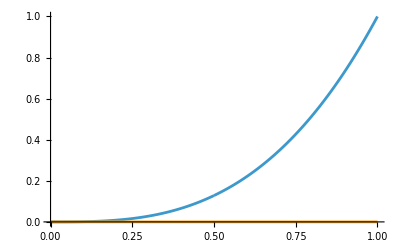

```mathematica
Subscript[z, h]=zh;
(*sl=F1H[c1,c2, ω,k][bound]//.result/.k->1/.c1->1//Quiet
sl1=F2H[czx,czy,vzx,vzy, ω,k][bound]/.k->1/.result//Quiet*)
Show[Plot[{htx[z]/.sl2//Re,htx[z]/.sl2//Im},{z,0,bound},PlotRange->All],Plot[{htx[z]/.sl1//Re,htx[z]/.sl1//Im},{z,bound,zh},PlotRange->All],PlotRange->All]/.zh->Subscript[z, h]
```

```mathematica
kn
```

2

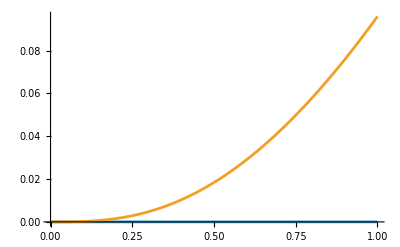

```mathematica
Show[Plot[{hyx[z]/.sl2//Re,hyx[z]/.sl2//Im},{z,0,bound},PlotRange->All],Plot[{(**)hyx[z]/.sl1//Re,hyx[z]/.sl1//Im},{z,bound,zh},PlotRange->All],PlotRange->All]/.zh->Subscript[z, h]
```

```mathematica
(*Extract the interpolation data points from f1 and f2*)
datahtx1=Table[{z,htx[z]/.sl2},{z,small,bound,(*choose an appropriate step size,e.g.,*)0.01}];
datahtx2=Table[{z,htx[z]/.sl1},{z,bound+0.01,1-smallIR,0.01}]; (*avoid redundancy at z=b*)

(*Combine the data from both interpolations*)
combinedDatahtx=Join[datahtx1,datahtx2];

(*Create a new interpolation function from the combined data*)
htxFunction2[z_]=Interpolation[combinedDatahtx];
```

```mathematica
htxFunction[z_]:=Piecewise[{{htx[z]/.sl2,z<bound},{htx[z]/.sl1,z>=bound}}];
hyxFunction[z_]:=Piecewise[{{hyx[z]/.sl2,z<bound},{hyx[z]/.sl1,z>=bound}}];
```

```mathematica
htxFunctionInterp=Interpolation[Table[{z,Evaluate[htxFunction[z]]},{z,0,zh,10^-4}]]/.zh->Subscript[z, h]//Quiet
```

```mathematica
InterpolatingFunction[…]
```

```mathematica
hyxFunctionInterp=Interpolation[Table[{z,Evaluate[hyxFunction[z]]},{z,0,zh,10^-4}]]/.zh->Subscript[z, h]//Quiet
```

```mathematica
InterpolatingFunction[…]
```

```mathematica
result
```

{c2→4.303243346625489395774491367576178558660651803419647566×10^-57+0.09592844298288872079150473928251225081831117028229054377 ⅈ,vty→1.07008752466623977356239970213344975035006088556619446-3.85475099833543823179881551194684471338407487913741777×10^-55 ⅈ,ω→1.619653875710039715614180009628978674517795156205189954×10^-64-0.1362518568851439731924017275660970681740422509016507181 ⅈ}

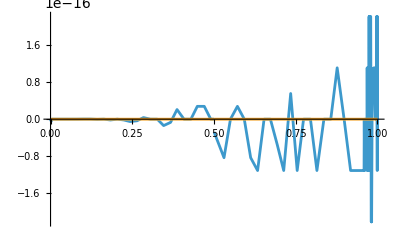

```mathematica
Plot[{(htxFunction[z]-htxFunctionInterp[z])//Re,(htxFunction[z]-htxFunctionInterp[z])//Im(*,hzxFunctionInterp[z]//Re,hzxFunction[z]//Im,hzxFunctionInterp[z]//Im*)},{z,0,1.0},PlotRange->All]
```

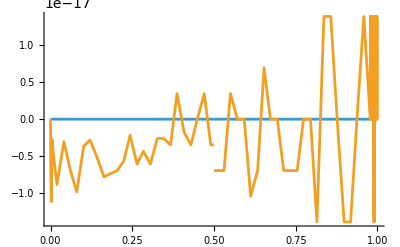

```mathematica
Plot[{(hyxFunction[z]-hyxFunctionInterp[z])//Re,(hyxFunction[z]-hyxFunctionInterp[z])//Im},{z,0,1.0},PlotRange->All]
```

### Energy Computation

#### htx And hzx

(ⅇ^(ⅈ k x3-ⅈ v ω) ϵ htx[z])/(2 z^2)

```mathematica
(*htx[v_,z_,x3_]=1/(2 z^2)htxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;
hzx[v_,z_,x3_]=1/(2 z^2)hzxFunction[z] E^(-I ω v+I k x3)/.k->1/.result;*)
```

```mathematica
ClearAll[hzx]
```

#### Master Scalar

```mathematica
gdd=G/.ϵ->0;
```

```mathematica
guu=IG/.ϵ->0;
```

```mathematica
ΓBG=Γ/.ϵ->0;
```

```mathematica
ClearAll[Φ]
```

```mathematica
CovCov=Sum[guu[[a,b]](D[D[Φ[v,z,x3], X[[a]]], X[[b]]]-Sum[Γ[[e,b,a]]D[Φ[v,z,x3], X[[e]]],{e,1,5}]),{a,1,5},{b,1,5}]//Simplify;
```

Part::partw: Part 5 of «1» does not exist.

Part::partw: Part 5 of {v,z,x1,x2} does not exist.

Part::partw: Part 5 of «1» does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Pot=k^2 z^2+z^2 D[f[z], z]z+(-f[z] z^2);
```

```mathematica
MasterEq=CovCov-(*V*)Pot Φ[v,z,x3](*/.k->1*);
```

```mathematica
Pot/.f->Function[z,1/z^2(1-z^4/zh^4)]//Series[#,{z,0,4}]&
```

-3+k^2 z^2-z^4+O[z]^5

```mathematica
MasterEq
```

```mathematica
Pot
```

k^2 z^2-z^2 f[z]+z^3 f'[z]

#### EF to FG

```mathematica
XFG={v+ Integrate[1/f[z],z],z,x1,x2,x3}
```

{v+∫1/f[z]ⅆz,z,x1,x2,x3}

```mathematica
X
```

{v,z,x1,x2}

```mathematica
JacobianFG=Table[D[XFG[[i]],X[[j]]],{i,1,5},{j,1,5}]; (*This computes a 5x5 Jacobian matrix*)
```

Part::partw: Part 5 of {v,z,x1,x2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
JacobianFG
```

{{1,1/f[z],0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,0}}

```mathematica
GFG=Table[Sum[JacobianFG[[u,a]] G[[u,vv]] JacobianFG[[vv,b]],{u,1,5},{vv,1,5}],{a,1,5},{b,1,5}]//Simplify;
GFGh=SeriesCoefficient[GFG,{ϵ,0,1}]//Normal;
GFGh//MatrixForm
```

Part::partw: Part 5 of {-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0} does not exist.

Part::partw: Part 5 of {-1/z^2,0,0,0} does not exist.

Part::partw: Part 5 of {(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

(0 | 0 | (ⅇ^(ⅈ (k x2-v ω)) htx[z])/(2 z^2) | 0 | 0
0 | 0 | (ⅇ^(ⅈ (k x2-v ω)) htx[z])/(2 z^2 f[z]) | 0 | 0
(ⅇ^(ⅈ (k x2-v ω)) htx[z])/(2 z^2) | (ⅇ^(ⅈ (k x2-v ω)) htx[z])/(2 z^2 f[z]) | 0 | (ⅇ^(ⅈ (k x2-v ω)) hyx[z])/(2 z^2) | 0
0 | 0 | (ⅇ^(ⅈ (k x2-v ω)) hyx[z])/(2 z^2) | 0 | 0
0 | 0 | 0 | 0 | 0)

#### H Curly FG

Already translated

```mathematica
HFGtz=GFGh[[1,3]]-D[GFGh[[3,5]]/(I k), v]//Simplify;
HFGrz=GFGh[[2,3]]+(z^2 D[GFGh[[3,5]]/(I k), z]-1/f[z] D[GFGh[[3,5]]/(I k), v])+2z GFGh[[3,5]]/(I k)//Simplify;
```

#### H Curly EF

```mathematica
HEFtz=HFGtz;
HEFrz=HFGrz-1/f[z] HFGtz;
```

#### Boundary conditions

```mathematica
Normal[Series[MasterEq/.Φ->Function[{v,z,x3},E^(-I ω v) z^(Δ(*-1/2*))]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.k->1/.ω->0/.zh->1,{z,0,1}]]//Simplify
```

Part::partw: Part 5 of {{0,-z^2,0,0},{-z^2,z^2 (1-z^4),0,0},{0,0,z^2,0},{0,0,0,z^2}} does not exist.

Part::partw: Part 5 of {-1/2 z^2 (-4 z-(2 (1-z^4))/z^3),0,(ⅇ^(ⅈ (k x2-v ω)) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0} does not exist.

Part::partw: Part 5 of {1/2 z^2 (1-z^4) (-4 z-(2 (1-z^4))/z^3),1/2 z^2 (-4 z-(2 (1-z^4))/z^3),-(ⅇ^(ⅈ (k x2-v ω)) (1-z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

z^(-1+Δ) (3 z-3 z Δ+z Δ^2-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦5,1⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,1,5⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦5,2⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,2,5⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦5,3⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,3,5⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦5,4⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,4,5⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦1,5⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,5,1⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦2,5⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,5,2⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦3,5⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,5,3⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦4,5⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,5,4⟧-Δ {{0,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}⟦5,5⟧ {{{1/z+z^3,0,(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{0,0,0,0},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-2 hyx[z]+z hyx'[z]))/(4 z),-1/z}},{{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3}},{{-(ⅇ^(ⅈ x2) (1+z^4) ϵ htx[z])/(2 z),(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z]},{(ⅇ^(ⅈ x2) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0,-1/z,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z]},{0,-1/z,(ⅇ^(ⅈ x2) ϵ htx[z])/(2 z),0},{1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,(ⅇ^(ⅈ x2) ϵ (htx[z]+ⅈ z hyx[z]))/(2 z)}},{{0,0,-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],0},{0,0,1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],-1/z},{-1/4 ⅈ ⅇ^(ⅈ x2) ϵ htx[z],1/4 ⅇ^(ⅈ x2) ϵ hyx'[z],0,0},{0,-1/z,0,0}}}⟦2,5,5⟧)

```mathematica
Solve[%==0,Δ]
```

Part::partw: Part 5 of {{(-1+z^8)/z,-(1+z^4)/z,(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),0},{-(1+z^4)/z,-2/z,-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],0},{(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[«1»]+z («1»)^(«1»)[«1»])))/(4 z)},{0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[«1»]+z («1»)^(«1»)[«1»])))/(4 z),1/z-z^3}} does not exist.

Part::partw: Part 5 of {0,0,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z),1/z-z^3} does not exist.

Part::partw: Part 5 of {(ⅇ^(ⅈ x2) (-1+z^4) ϵ (-2 htx[z]+z htx'[z]))/(4 z),-1/4 ⅇ^(ⅈ x2) ϵ htx'[z],1/z-z^3,(ⅇ^(ⅈ x2) ϵ (-ⅈ z htx[z]+(-1+z^4) (-2 hyx[z]+z hyx'[z])))/(4 z)} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
ΦExp=Function[z, Sum[p[i] z^i,{i,1,7}]];
```

```mathematica
hhtxExp=(ⅇ^(ⅈ k x3-ⅈ v ω) Ashtx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
hhzxExp=(ⅇ^(ⅈ k x3-ⅈ v ω) Ashzx[czx,vzx, ω,k][z])/(2 z^2)(*/.result*);
```

To check

```mathematica
hEFrzEXP=HEFrz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]](*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
EXPEq=hEFrzEXP==(ⅇ^(ⅈ k x3-ⅈ v ω)D[ΦExp[z], z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]);
```

```mathematica
(*z^2∂_z hhzxExp+2 z hhzxExp-1/f[z](hhtxExp-∂_v hhzxExp)==(HEFrz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1//Simplify*)
```

```mathematica
EXPEq2=(HEFtz/.hzx->Function[z,Ashzx[czx,vzx, ω,k][z]]/.htx->Function[z,Ashtx[czx,vzx, ω,k][z]])(*hhtxExp-∂_v hhzxExp*)==3 f[z]/z ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]+f[z]/z^2(-z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), z])+1/z^2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)ΦExp[z]), v]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1;
```

```mathematica
p1Rule=Solve[Series[{EXPEq},{z,0,0}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-2}]//Normal,p[1]]//Flatten(*//Simplify*)
```

{p[1]→1/4 ⅇ^(ⅈ k x2-ⅈ k x3) Ashtx[czx,vzx,ω,k][0]}

```mathematica
p2Rule=Solve[Series[EXPEq,{z,0,1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→0}

```mathematica
Solve[Series[EXPEq2,{z,0,-1}]/.p1Rule//Normal,p[2]]//Flatten
```

{p[2]→(ⅇ^(ⅈ k x2-ⅈ k x3) (Ashtx[czx,vzx,ω,k][0]+z Ashtx[czx,vzx,ω,k]'[0]))/(2 z)}

```mathematica
Solve[Series[EXPEq,{z,0,2}]/.p1Rule/.p2Rule//Normal,p[3]]//Flatten
```

{}

```mathematica
p4Rule=Solve[Series[EXPEq,{z,0,3}](*/.p3Rule*)/.p1Rule/.p2Rule//Normal,p[4]]//Flatten
```

{p[4]→0}

```mathematica
p5Rule=Solve[Series[EXPEq,{z,0,4}]/.p4Rule/.p1Rule/.p2Rule(*/.p3Rule*)//Normal,p[5]]//Flatten
```

{p[5]→0}

```mathematica
p6Rule=Solve[Series[EXPEq,{z,0,5}]/.p5Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule//Normal,p[6]]//Simplify//Flatten
```

{p[6]→0}

```mathematica
p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p6Rule/.p1Rule/.p2Rule(*/.p3Rule*)/.p4Rule/.p5Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten
```

{p[7]→0}

```mathematica
p3Rule=Solve[Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p4Rule//Normal,p[3]]//Flatten(*//Simplify*)
```

{p[3]→(ⅈ ⅇ^(ⅈ k x2-ⅈ k x3) (6 Ashtx[czx,vzx,ω,k][0]+6 z Ashtx[czx,vzx,ω,k]'[0]+3 z^2 Ashtx[czx,vzx,ω,k]''[0]+z^3 Ashtx[czx,vzx,ω,k]^(3)[0]))/(12 z^3 ω)}

consistency check

```mathematica
Series[EXPEq2,{z,0,1}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule//Normal
```

(ⅇ^(ⅈ (k x2-v ω)) Ashtx[czx,vzx,ω,k][0])/(2 z^2)+(ⅇ^(ⅈ (k x2-v ω)) Ashtx[czx,vzx,ω,k]'[0])/(2 z)+1/4 ⅇ^(ⅈ (k x2-v ω)) Ashtx[czx,vzx,ω,k]''[0]+1/12 ⅇ^(ⅈ (k x2-v ω)) z Ashtx[czx,vzx,ω,k]^(3)[0]==(ⅇ^(ⅈ k x2-ⅈ v ω) Ashtx[czx,vzx,ω,k][0])/(2 z^2)+(ⅇ^(ⅈ k x2-ⅈ v ω) Ashtx[czx,vzx,ω,k]'[0])/(2 z)+1/4 ⅇ^(ⅈ k x2-ⅈ v ω) Ashtx[czx,vzx,ω,k]''[0]+1/12 ⅇ^(ⅈ k x2-ⅈ v ω) z Ashtx[czx,vzx,ω,k]^(3)[0]

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

ⅇ^(ⅈ (k x2-v ω)) z Ashtx[czx,vzx,ω,k]^(4)[0]==0

```mathematica
Series[EXPEq2,{z,0,2}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule//Normal//Simplify
```

ⅇ^(ⅈ (k x2-v ω)) z Ashtx[czx,vzx,ω,k]^(4)[0]==0

```mathematica
Series[EXPEq2,{z,0,3}]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal//Simplify
```

ⅇ^(ⅈ (k x2-v ω)) z (5 Ashtx[czx,vzx,ω,k]^(4)[0]+z Ashtx[czx,vzx,ω,k]^(5)[0])==0

```mathematica
(*p7Rule=Solve[Series[EXPEq,{z,0,6}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule//Normal,p[7]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p8Rule=Solve[Series[EXPEq,{z,0,7}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule//Normal,p[8]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
(*p9Rule=Solve[Series[EXPEq,{z,0,8}]/.p0Rule/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.p8Rule//Normal,p[9]](*/.result/.k->1*)//Simplify//Flatten*)
```

```mathematica
ClearAll[ΦExpBC]
```

```mathematica
ΦExpBC[zz_]:=ΦExp[z]/.p1Rule/.p2Rule/.p3Rule/.p4Rule/.p5Rule/.p6Rule/.p7Rule/.result/.k->1/.z->zz
```

```mathematica
ΦExpBC[small]
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

(ⅈ ⅇ^(ⅈ x2-ⅈ x3) (6 Ashtx[czx,vzx,ω,1][0]+(3 Ashtx[czx,vzx,ω,1]'[0])/500000+(3 Ashtx[czx,vzx,ω,1]''[0])/1000000000000+(Ashtx[czx,vzx,ω,1]^(3)[0])/1000000000000000000))/(12 ω)/.1

```mathematica
D[ΦExpBC[z], z]/.z->small
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

General::ivar: 1/1000000 is not a valid variable.

∂_(1/1000000) ((ⅈ ⅇ^(ⅈ x2-ⅈ x3) (6 Ashtx[czx,vzx,ω,1][0]+(3 Ashtx[czx,vzx,ω,1]'[0])/500000+(3 Ashtx[czx,vzx,ω,1]''[0])/1000000000000+(Ashtx[czx,vzx,ω,1]^(3)[0])/1000000000000000000))/(12 ω)/.1)

#### Differential Equation for Φ

```mathematica
hhzx[v_,z_,x3_]:=ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)hzxFunction[z];
hhtx[v_,z_,x3_]:=ⅇ^(ⅈ k x3-ⅈ v ω)/(2 z^2)htxFunction[z];
```

```mathematica
(*ClearAll[hhzx,hhtx]*)
```

```mathematica
(*z^2∂_z hhzxExp(I k)^-1+2 z hhzxExp(I k)^-1-1/f[z](hhtxExp-∂_v hhzxExp(I k)^-1)*)
```

```mathematica
HEFrz
```

0

```mathematica
ΦEqLHS=HEFrz/.htx->Function[z,htxFunction[z]]/.hzx->Function[z,hzxFunction[z]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1(*/.k->1*);
ΦEqRHS=(ⅇ^(ⅈ k x3-ⅈ v ω)D[(z^3 Φ[z]), z]-3/z ⅇ^(ⅈ k x3-ⅈ v ω)(z^3 Φ[z]))/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/.k->1(*/.x3->0*)/.v->0(*/.ω->0*)/.result(*//Simplify*);
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
ΦEq=(ΦEqLHS/.zh->1/.k->1/.x3->0/.v->0/.result)==(ΦEqRHS/.zh->1/.k->1/.x3->0/.v->0/.result);
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
ΦEqRHS
```

-3 ⅇ^(ⅈ x3) z^2 Φ[z]+ⅇ^(ⅈ x3) (3 z^2 Φ[z]+z^3 Φ'[z])/.1

```mathematica
ΦFunction=Φ/.(NDSolve[{ΦEq,Φ[small]==ΦExpBC[small]/small^3(*,Φ'[small]==∂_z ΦExpBC[z]/.z->small*)},Φ,{z,small,1-smallIR},WorkingPrecision->30]//Flatten)
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndinnt: Initial condition 1.×10^18 ((0.0833333333333333333333333333333 ⅈ («64»)^(«1»-«1») (6. Ashtx[czx,vzx,ω,1.][0]+6.×10^-6 Ashtx[czx,vzx,ω,1.]'[0]+«57» Ashtx[czx,«3»]''[0]+1.×10^-18 Ashtx[czx,vzx,ω,1.]^(3)[0]))/ω/.1.) is not a number or a rectangular array of numbers.

Φ/.NDSolve[{(0/.1)==(z^3 Φ'[z]/.1/.1),Φ[1/1000000]==1000000000000000000 ((ⅈ ⅇ^(ⅈ x2-ⅈ x3) (6 Ashtx[czx,vzx,ω,1][0]+(3 Ashtx[czx,vzx,ω,1]'[0])/500000+(3 Ashtx[czx,vzx,ω,1]''[0])/1000000000000+(Ashtx[czx,vzx,ω,1]^(3)[0])/1000000000000000000))/(12 ω)/.1)},Φ,{z,1/1000000,9999999999/10000000000},WorkingPrecision→30]

```mathematica
Plot[{(ΦFunction[z])//Re,(ΦFunction[z])//Im},{z,0,1},PlotRange->All]
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000204286 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{(0/.1)==(8.52538×10^-15 («1»)^(«1»)[«1»]/.1/.1),Φ[1/1000000]==1000000000000000000 (1/12 ⅈ Power[«2»] Power[«2»] Plus[«4»]/.1)},Φ,{0.0000204286,1/1000000,9999999999/10000000000},WorkingPrecision→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

NDSolve::dsvar: 0.0000204286 cannot be used as a variable.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

NDSolve::dsvar: 0.0204286 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

-Graphics-

#### Energy

```mathematica
ClearAll[Tdd]
```

```mathematica
Tdd=Table[1/2 D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[a]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]), X[[b]]]])+1/2 1/2  (Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[a]]]])D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[b]]]-(G[[a,b]]/.ϵ->0)(Sum[IG[[c,cc]]D[(ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z]), X[[c]]](Conjugate[D[(z^3 ⅇ^(ⅈ k x3-ⅈ v ω) Φ[z]), X[[cc]]]]),{cc,1,5},{c,1,5}]+Pot ⅇ^(ⅈ k x3-ⅈ v ω)z^3 Φ[z] z^3 (Conjugate[ⅇ^(ⅈ k x3-ⅈ v ω)Φ[z]])),{a,1,5},{b,1,5}]/.result/.k->1/.x3->0/.v->0/.ϵ->0/.f->Function[z,1/z^2(1-z^4/zh^4)]/.zh->1/. Φ->Function[z,ΦFunction[z]];
```

Part::partw: Part 5 of … does not exist.

Part::partw: Part 5 of {v,z,x1,x2} does not exist.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndinnt: Initial condition 1.×10^18 ((0.0833333333333333333333333333333 ⅈ («64»)^(«1»-«1») (6. Ashtx[czx,vzx,ω,1.][0]+6.×10^-6 Ashtx[czx,vzx,ω,1.]'[0]+«57» Ashtx[czx,«3»]''[0]+1.×10^-18 Ashtx[czx,vzx,ω,1.]^(3)[0]))/ω/.1.) is not a number or a rectangular array of numbers.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

I define a tangent vector ξ coming from (∂x^μ)/(∂λ) (where in the parametrization x^μ=0,λ,0,0,0) and the surface element dΣ_μ=r^2 dr dx_1 dx_2 dx_3∂_μ Φ, where Φ is the equation of the hypersurface Φ=v-constant=0. So dΣ_μ is going to be in the direction of v. Then I convert  r=1/z and dr=-1/z^2 dz

```mathematica
ξu={0,1,0,0,0};
dΣu=-1/z^4 IG.{1,0,0,0,0}/.ϵ->0;
```

Dot::dotsh: Tensors … and {1,0,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{0,-z^2,0,0},{-z^2,z^4 f[z],0,0},{0,0,z^2,0},{0,0,0,z^2}} and {1,0,0,0,0} have incompatible shapes.

```mathematica
G.ξu.dΣu/.f->Function[z,1/z^2(1-z^4/zh^4)]/.ϵ->0//Simplify
```

Dot::dotsh: Tensors {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} and {0,1,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{0,-z^2,0,0},{-z^2,z^2 (1-z^4),0,0},{0,0,z^2,0},{0,0,0,z^2}} and {1,0,0,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{-(1-z^4)/z^2,-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} and {0,1,0,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

{{(-1+z^4)/z^2,-1/z^2,0,0},{-1/z^2,0,0,0},{0,0,1/z^2,0},{0,0,0,1/z^2}}.{0,1,0,0,0}.(-({{0,-z^2,0,0},{-z^2,z^2-z^6,0,0},{0,0,z^2,0},{0,0,0,z^2}}.{1,0,0,0,0})/z^4)

```mathematica
ClearAll[Integrand]
```

```mathematica
Integrand[zz_]:=Sum[Tdd[[a,b]]ξu[[a]]dΣu[[b]]/.f->Function[z,1/z^2(1-z^4/zh^4)]/.v->0/.zh->1/.k->1/.x3->0,{a,1,5},{b,1,5}]/.result/.z->zz//Simplify
```

Below I compute the energy per spatial voume. It ha s to be multiplied by a factor L^3

```mathematica
NIntegrate[Abs[Integrand[z]],{z,0,1}]
```

ReplaceAll::reps: {1} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndinnt: Initial condition 1.×10^18 ((0.0833333333333333333333333333333 ⅈ («64»)^(«1»-«1») (6. Ashtx[czx,vzx,ω,1.][0]+6.×10^-6 Ashtx[czx,vzx,ω,1.]'[0]+«57» Ashtx[czx,«3»]''[0]+1.×10^-18 Ashtx[czx,vzx,ω,1.]^(3)[0]))/ω/.1.) is not a number or a rectangular array of numbers.

ReplaceAll::reps: {NDSolve[{(0/.1)==(Power[«2»] («1»)^(«1»)[«1»]/.1/.1),Φ[1/1000000]==1000000000000000000 (1/12 ⅈ Power[«2»] Power[«2»] Plus[«4»]/.1)},Φ,{z,1/1000000,9999999999/10000000000},WorkingPrecision→30]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::argx: ReplaceAll called with 2 arguments; 1 argument is expected.

General::stop: Further output of ReplaceAll::argx will be suppressed during this calculation.

Part::partw: Part 5 of {-(1-z^4)/z^2,-1/z^2,0,0} does not exist.

Part::partw: Part 5 of {-1/z^2,0,0,0} does not exist.

Part::partw: Part 5 of {0,0,1/z^2,0} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Dot::dotsh: Tensors {{0,-z^2,0,0},{-z^2,z^4 f[z],0,0},{0,0,z^2,0},{0,0,0,z^2}} and {1,0,0,0,0} have incompatible shapes.

Part::partd: Part specification … is longer than depth of object.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

NDSolve::ndinnt: Initial condition 1.×10^18 ((0.0833333333333333333333333333333 ⅈ («64»)^((«1») x2) (6. Ashtx[czx,vzx,ω,1.][0]+6.×10^-6 Ashtx[czx,vzx,ω,1.]'[0]+«57» Ashtx[czx,«3»]''[0]+1.×10^-18 Ashtx[czx,vzx,ω,1.]^(3)[0]))/ω/.1.) is not a number or a rectangular array of numbers.

NDSolve::ntdvdae: Cannot solve to find an explicit formula for the derivatives. NDSolve will try solving the system as differential-algebraic equations.

General::stop: Further output of NDSolve::ntdvdae will be suppressed during this calculation.

NDSolve::ndinnt: Initial condition 1.×10^18 ((0.0833333333333333333333333333333 ⅈ («64»)^((«1») x2) (6. Ashtx[czx,vzx,ω,1.][0]+6.×10^-6 Ashtx[czx,vzx,ω,1.]'[0]+«57» Ashtx[czx,«3»]''[0]+1.×10^-18 Ashtx[czx,vzx,ω,1.]^(3)[0]))/ω/.1.) is not a number or a rectangular array of numbers.

General::stop: Further output of NDSolve::ndinnt will be suppressed during this calculation.

Part::partd: Part specification … is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Dot::dotsh: Tensors {{0,-z^2,0,0},{-z^2,z^2 (1-z^4),0,0},{0,0,z^2,0},{0,0,0,z^2}} and {1,0,0,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

NIntegrate::inumr: The integrand Abs[«1»] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,1}}.

NIntegrate[Abs[Integrand[z]],{z,0,1}]

Check that ξ and dΣ are orthogonal

#### Getting the radial profile of ξ

```mathematica
exponential=Exp[-I ω  v] ⅇ^(ⅈ k x3);
```

```mathematica
ξu= ϵ exponential{0,0,ζ3[z], 0,0};
ξd=G.ξu;
```

Dot::dotsh: Tensors {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} and {0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3[z],0,0} have incompatible shapes.

```mathematica
ξd
```

{{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}}.{0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3[z],0,0}

```mathematica
Dξd=Table[1/2(D[ξd[[i]],X[[j]]]+D[ξd[[j]],X[[i]]])-Sum[Γ[[kk,i,j]] ξd[[kk]],{kk,1,5}],{i,1,5},{j,1,5}];
```

Part::partw: Part 3 of {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}}.{0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3[z],0,0} does not exist.

Part::partw: Part 4 of {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}}.{0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3[z],0,0} does not exist.

Part::partw: Part 5 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

Thread::tdlen: Objects of unequal length in {{0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω htx[z])/(2 z^2),0},{0,0,0,0},{-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω htx[z])/(2 z^2),0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω hyx[z])/(2 z^2)},{0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω hyx[z])/(2 z^2),0}}+«6» cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

Dot::dotsh: Tensors {{0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω htx[z])/(2 z^2),0},{0,0,0,0},{-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω htx[z])/(2 z^2),0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω hyx[z])/(2 z^2)},{0,0,-(ⅈ ⅇ^(ⅈ k x2-ⅈ v ω) ϵ ω hyx[z])/(2 z^2),0}} and {0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3[z],0,0} have incompatible shapes.

Dot::dotsh: Tensors {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} and {0,0,-ⅈ ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ω ζ3[z],0,0} have incompatible shapes.

Dot::dotsh: Tensors {{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} and {0,0,ⅇ^(ⅈ k x3-ⅈ v ω) ϵ ζ3'[z],0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

```mathematica
Gξd=Series[Simplify[2 Dξd]+G,{ϵ,0,1}]//Normal//Simplify;
```

Thread::tdlen: Objects of unequal length in {«1»}+{{-f[z],-1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ htx[z])/(2 z^2),0,1/z^2,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2)},{0,0,(ⅇ^(ⅈ k x2-ⅈ v ω) ϵ hyx[z])/(2 z^2),1/z^2}} cannot be combined.

Dot::dotsh: Tensors {{-f[z],-1/z^2,(ⅇ^(ⅈ Plus[«2»]) htx[z] ϵ)/(2 z^2)+O[ϵ]^2,0},{-1/z^2,0,0,0},{(ⅇ^(ⅈ Plus[«2»]) htx[z] ϵ)/(2 z^2)+O[ϵ]^2,0,1/z^2,(ⅇ^(ⅈ Plus[«2»]) hyx[z] ϵ)/(2 z^2)+O[ϵ]^2},{0,0,(ⅇ^(ⅈ Plus[«2»]) hyx[z] ϵ)/(2 z^2)+O[ϵ]^2,1/z^2}} and {0,0,ⅇ^(ⅈ (Times[«2»]+Times[«3»])) ζ3[z] ϵ+O[ϵ]^2,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{-f[z],-1/z^2,#1,0},{-1/z^2,0,0,0},{#2,0,1/z^2,#3},{0,0,#4,1/z^2}} and {0,0,#5,0,0} have incompatible shapes.

Dot::dotsh: Tensors {{-f[z],-1/z^2,0,0},{-1/z^2,0,0,0},{0,0,1/z^2,0},{0,0,0,1/z^2}} and {0,0,0,0,0} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Part::partw: Part 5 of {{-f[z],-1/z^2,0,0},{-1/z^2,0,0,0},{0,0,1/z^2,0},{0,0,0,1/z^2}}.{0,0,0,0,0} does not exist.

Part::partw: Part 5 of … does not exist.

Part::partw: Part 5 of {{{-1/2 z^2 f'[z],0,#1,0},{0,0,0,0},{#2,0,-1/z,#3},{0,0,#4,-1/z}},{{1/2 z^4 f[z] f'[z],1/2 z^2 f'[z],#5,0},{1/2 z^2 f'[z],-2/z,#6,0},{#7,#8,z f[z],#9},{0,0,#10,z f[z]}},{{#11,#12,0,#13},{#14,0,-1/z,#15},{0,-1/z,#16,0},{#17,#18,0,#19}},{{0,0,#20,0},{0,0,#21,-1/z},{#22,#23,0,0},{0,-1/z,0,0}}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Thread::tdlen: Objects of unequal length in … cannot be combined.

General::stop: Further output of Thread::tdlen will be suppressed during this calculation.

$Aborted

```mathematica
Gξd//MatrixForm
```

(-f[z] | -1/z^2 | (ⅇ^(ⅈ (k x3-v ω)) ϵ (htx[z]-2 ⅈ ω ζ3[z]))/(2 z^2) | 0 | 0
-1/z^2 | 0 | (ⅇ^(ⅈ (k x3-v ω)) ϵ ζ3'[z])/z^2 | 0 | 0
(ⅇ^(ⅈ (k x3-v ω)) ϵ (htx[z]-2 ⅈ ω ζ3[z]))/(2 z^2) | (ⅇ^(ⅈ (k x3-v ω)) ϵ ζ3'[z])/z^2 | 1/z^2 | 0 | (ⅇ^(ⅈ (k x3-v ω)) ϵ (hzx[z]+2 ⅈ k ζ3[z]))/(2 z^2)
0 | 0 | 0 | 1/z^2 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) ϵ (hzx[z]+2 ⅈ k ζ3[z]))/(2 z^2) | 0 | 1/z^2)

```mathematica
({{-f[z], -1/z^2, (ⅇ^(ⅈ (k x3-v ω)) ϵ (htx[z]-2 ⅈ ω ζ3[z]))/(2 z^2), 0, 0}, {-1/z^2, 0, (ⅇ^(ⅈ (k x3-v ω)) ϵ ζ3'[z])/z^2, 0, 0}, {(ⅇ^(ⅈ (k x3-v ω)) ϵ (htx[z]-2 ⅈ ω ζ3[z]))/(2 z^2), (ⅇ^(ⅈ (k x3-v ω)) ϵ ζ3'[z])/z^2, 1/z^2, 0, (ⅇ^(ⅈ (k x3-v ω)) ϵ (hzx[z]+2 ⅈ k ζ3[z]))/(2 z^2)}, {0, 0, 0, 1/z^2, 0}, {0, 0, (ⅇ^(ⅈ (k x3-v ω)) ϵ (hzx[z]+2 ⅈ k ζ3[z]))/(2 z^2), 0, 1/z^2}})/.ζ3->Function[z,(ⅈ czx)/(2 k)]//Simplify//MatrixForm
```

(-f[z] | -1/z^2 | (ⅇ^(ⅈ (k x3-v ω)) ϵ ((czx ω)/k+htx[z]))/(2 z^2) | 0 | 0
-1/z^2 | 0 | 0 | 0 | 0
(ⅇ^(ⅈ (k x3-v ω)) ϵ ((czx ω)/k+htx[z]))/(2 z^2) | 0 | 1/z^2 | 0 | (ⅇ^(ⅈ (k x3-v ω)) ϵ (-czx+hzx[z]))/(2 z^2)
0 | 0 | 0 | 1/z^2 | 0
0 | 0 | (ⅇ^(ⅈ (k x3-v ω)) ϵ (-czx+hzx[z]))/(2 z^2) | 0 | 1/z^2)

```mathematica
IGξ=Inverse[Gξd]//Simplify;
IGξ/.ϵ->0//MatrixForm;
```

```mathematica
IGξ.Gξd//Simplify
```

{{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}

```mathematica
Γξ=Normal[Series[Table[1/2*Sum[IGξ[[i,l]]*(D[Gξd[[j,l]],X[[k1]]]+D[Gξd[[k1,l]],X[[j]]]-D[Gξd[[j,k1]],X[[l]]]),{l,1,d}],{i,1,d},{j,1,d},{k1,1,d}],{ϵ,0,1}]]//Simplify;//AbsoluteTiming
```

{0.237466,Null}

```mathematica
Ricξ=Table[Sum[D[Γξ[[k1,i,j]],X[[k1]]]-D[Γξ[[k1,k1,i]],X[[j]]]+Sum[Γξ[[q1,q1,k1]]Γξ[[k1,i,j]]-Γξ[[q1,i,k1]]Γξ[[k1,q1,j]],{q1,1,d}],{k1,1,d}],{i,1,d},{j,1,d}]//Simplify;//AbsoluteTiming
```

{0.9176,Null}

```mathematica
Rξ=Normal[Series[Sum[IGξ[[i,j]]Ricξ[[i,j]],{i,1,d},{j,1,d}],{ϵ,0,1}]]//Simplify;//AbsoluteTiming
```

{0.027455,Null}

```mathematica
Ric//Dimensions
```

{5,5}

```mathematica
EinEqξ=Normal[Series[Ricξ+4 Gξd,{ϵ,0,1}]]/.f->Function[z,1/z^2(1-z^4/zh^4)](*/.f->Function[z,1-z^4/zh^4]*)/.zh->1//Simplify;//AbsoluteTiming
EinEqξ/.ϵ->0//Expand//Simplify//MatrixForm
```

{0.012922,Null}

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

```mathematica
EinEqξ[[1,3]]
EinEqξ[[2,3]]
EinEqξ[[3,5]]
```

(ⅇ^(ⅈ (k x3-v ω)) ϵ (k^2 z htx[z]+k z ω hzx[z]+3 htx'[z]-3 z^4 htx'[z]-ⅈ z ω htx'[z]-z htx''[z]+z^5 htx''[z]))/(4 z)

(ⅇ^(ⅈ (k x3-v ω)) ϵ (3 htx'[z]+ⅈ k z hzx'[z]-z htx''[z]))/(4 z)

(ⅇ^(ⅈ (k x3-v ω)) ϵ (3 ⅈ k htx[z]+3 ⅈ ω hzx[z]-ⅈ k z htx'[z]+3 hzx'[z]+z^4 hzx'[z]-2 ⅈ z ω hzx'[z]-z hzx''[z]+z^5 hzx''[z]))/(4 z)

### Obair Gharbh

```mathematica
Solve[(Cos[2 Pi k (y-yMid)/(yMax-yMin)])==Cos[kM y],kM]//FullSimplify
```

{{kM→ConditionalExpression[(-ArcCos[Cos[(2 k π (y-yMid))/(yMax-yMin)]]+2 π C[1])/y, C[1]∈ℤ]},{kM→ConditionalExpression[(ArcCos[Cos[(2 k π (y-yMid))/(yMax-yMin)]]+2 π C[1])/y, C[1]∈ℤ]}}

```mathematica
((2 k π (y-yMid))/(yMax-yMin))/y//FullSimplify
```

(2 k π (y-yMid))/(y (yMax-yMin))